```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.6.2 (June 29, 2021)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

## Model setup and test case

```mathematica
Clear[r];
SetModel[{
Guild[n]->{
Equation:>(r[Subscript[x, i]]-Sum[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],{j,Subscript[𝒩, n]}])Subscript[n, i],
Traits->{x}
},
Parameters:>{w}
}];
```

```mathematica
mc=2*1.0470605718246615; (* magic constant *)
a[x_,y_]:=Exp[-(x-y)^2];
r[x_]:= 1.1Exp[-((x/w*mc)-0.5)^2/(2 σe^2)]+ 1.1Exp[-((x/w*mc)+0.5)^2/(2 σe^2)]-0.10037;
```

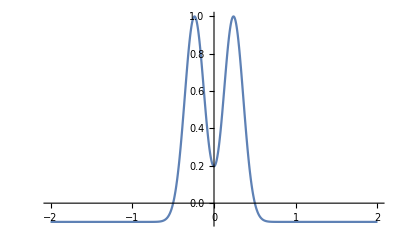

```mathematica
Clear[w];
σe=0.25;
w=1;
Plot[r[x],{x,-2,2}]
```

```mathematica
(*Starting at an equilibrium*)
```

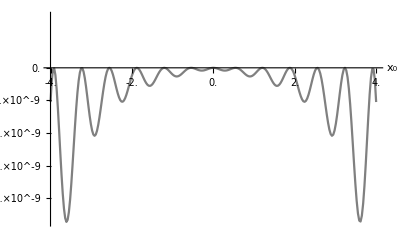

```mathematica
w=18.104702148436324;
init={Subscript[n, 1]->0.0926199572295689,Subscript[n, 2]->0.3054467336123645,Subscript[n, 3]->0.3054467336123572,Subscript[n, 4]->0.09261995722959782,Subscript[n, 5]->0.19960833729075528,Subscript[n, 6]->0.19960833729084695,Subscript[n, 7]->0.38614697666444503,Subscript[n, 8]->0.38614697666389675,Subscript[n, 9]->0.42238080805053163,Subscript[n, 10]->0.42238080804904043,Subscript[n, 11]->0.40766942213089497,Subscript[n, 12]->0.4076694221291592,Subscript[n, 13]->0.350143565345055,Subscript[n, 14]->0.35014356534602253,Subscript[n, 15]->0.2681225612865893,Subscript[n, 16]->0.26812256129589973,Subscript[n, 17]->0.18271526227816867,Subscript[n, 18]->0.1827152623027101,Subscript[n, 19]->0.11132970531997989,Subscript[n, 20]->0.11132970537682096,Subscript[n, 21]->0.06286824642034428,Subscript[n, 22]->0.06286824659834016,Subscript[n, 23]->0.040275275429342124,Subscript[x, 1]->-7.797255934807216,Subscript[x, 2]->6.10359936714411,Subscript[x, 3]->-6.103599367144485,Subscript[x, 4]->7.797255934807108,Subscript[x, 5]->-6.910090880025916,Subscript[x, 6]->6.910090880025615,Subscript[x, 7]->-5.3463294603132265,Subscript[x, 8]->5.34632946031337,Subscript[x, 9]->-4.621697695840446,Subscript[x, 10]->4.621697695842284,Subscript[x, 11]->-3.9193793693855334,Subscript[x, 12]->3.919379369390361,Subscript[x, 13]->-3.2320797024683667,Subscript[x, 14]->3.232079702475359,Subscript[x, 15]->-2.5539505928320807,Subscript[x, 16]->2.553950592829544,Subscript[x, 17]->-1.8796411380304139,Subscript[x, 18]->1.879641137966646,Subscript[x, 19]->-1.2048944168266627,Subscript[x, 20]->1.204894416492601,Subscript[x, 21]->-0.5445571482950136,Subscript[x, 22]->0.5445571466953067,Subscript[x, 23]->-1.9293529578842276*^-9};
PlotInv[init,{Subscript[x, 0],-4,4}]
```

```mathematica
(*FindEcoEvoEq works*)
w=18.104702148436324;
FindEcoEvoEq[init]
```

{n_1→0.09262,n_2→0.305447,n_3→0.305447,n_4→0.09262,n_5→0.199608,n_6→0.199608,n_7→0.386147,n_8→0.386147,n_9→0.422381,n_10→0.422381,n_11→0.407669,n_12→0.407669,n_13→0.350144,n_14→0.350144,n_15→0.268123,n_16→0.268123,n_17→0.182715,n_18→0.182715,n_19→0.11133,n_20→0.11133,n_21→0.0628682,n_22→0.0628682,n_23→0.0402753,x_1→-7.79726,x_2→6.1036,x_3→-6.1036,x_4→7.79726,x_5→-6.91009,x_6→6.91009,x_7→-5.34633,x_8→5.34633,x_9→-4.6217,x_10→4.6217,x_11→-3.91938,x_12→3.91938,x_13→-3.23208,x_14→3.23208,x_15→-2.55395,x_16→2.55395,x_17→-1.87964,x_18→1.87964,x_19→-1.20489,x_20→1.20489,x_21→-0.544557,x_22→0.544557,x_23→0}

```mathematica
(*Tracking fails*)
Clear[w];
TrackEcoEvoEq[init,{w,18.104702148436324,20.0,0.001}(*,MaxSteps-> 100*)];
```

$Aborted

```mathematica
Inv[{Subscript[𝒩, n]->2}]
```

Simplify::gtime: Returning the simplest form found in the allowed time of 0.01 seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

-0.10037+1.1 ⅇ^(-8. (-0.5+0.115667 x_0)^2)+1.1 ⅇ^(-8. (0.5+0.115667 x_0)^2)-ⅇ^(-(x_0-x_1)^2) n_1-ⅇ^(-(x_0-x_2)^2) n_2

```mathematica
FullSimplify[Inv[{Subscript[𝒩, n]->2}]]
```

Simplify::gtime: Returning the simplest form found in the allowed time of 0.01 seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

-0.10037+0.297738 ⅇ^(-0.107031 x_0^2) Cosh[0.925338 x_0]-ⅇ^(-(x_0-x_1)^2) n_1-ⅇ^(-(x_0-x_2)^2) n_2

```mathematica
FullSimplify[Inv[{Subscript[𝒩, n]->3}]]
```

Simplify::gtime: Returning the simplest form found in the allowed time of 0.01 seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

-0.10037+0.297738 ⅇ^(-0.107031 x_0^2) Cosh[0.925338 x_0]-ⅇ^(-(x_0-x_1)^2) n_1-ⅇ^(-(x_0-x_2)^2) n_2-ⅇ^(-(x_0-x_3)^2) n_3